```mathematica
ds=0.001;s9=Range[ds,1-ds,ds];num=Length[s9]; 
ones[n_]:=1+0Range[n];
```

```mathematica
psq=1/ds^2(2 DiagonalMatrix[ones[num]]-DiagonalMatrix[ones[num-1],1]-DiagonalMatrix[ones[num-1],-1]);
```

```mathematica
{eval,evec}=Eigensystem[1/2 psq+1/2 psq+DiagonalMatrix[1/2 π^4/4 s9^2]];
```

```mathematica
in=Ordering[eval];eval=eval⟦in⟧;evec=evec⟦in⟧;

evec⟦;;1⟧;
eval⟦;;10⟧
```

{13.1511,43.4238,92.8451,161.95,250.781,359.346,487.644,635.676,803.44,990.935}

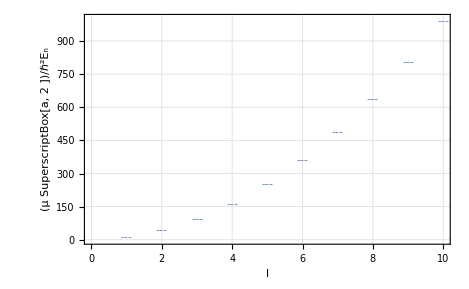

```mathematica
ThadPlot[ListPlot[eval⟦;;10⟧,PlotRange->{0,1000},PlotMarkers->"---"],{"l","(μ SuperscriptBox[a, 2 ])/ℏ^2E_n"}]
```

```mathematica
DSolve[{-1/2 P''[r]+((l(l+1))/(2 r^2)+1/6 π^5 r^2)P[r]== ϵ P[r]},P[r],r]
```

{{P[r]→(2^(1/4 (1-2 l)) ⅇ^(-(π^(5/2) r^2)/(2 √3)) (r^2)^(1/4 (1-2 l)) C[1] HypergeometricU[(π^(5/2)-2 l π^(5/2)-2 √3 ϵ)/(4 π^(5/2)),1/2 (1-2 l),(π^(5/2) r^2)/(√3)])/(√r)+(2^(1/4 (1-2 l)) ⅇ^(-(π^(5/2) r^2)/(2 √3)) (r^2)^(1/4 (1-2 l)) C[2] LaguerreL[-(π^(5/2)-2 l π^(5/2)-2 √3 ϵ)/(4 π^(5/2)),-1+1/2 (1-2 l),(π^(5/2) r^2)/(√3)])/(√r)}}

For n_x:

```mathematica
elevelsX=Table[{l,BesselJZero[1/2 (1-2 l),n+1]^2//N},{l,0,3},{n,0,5}]~Flatten~1
```

{{0,9.8696},{0,39.4784},{0,88.8264},{0,157.914},{0,246.74},{0,355.306},{1,2.4674},{1,22.2066},{1,61.685},{1,120.903},{1,199.859},{1,298.556},{2,7.83096},{2,7.83096},{2,37.4697},{2,86.8226},{2,155.912},{2,244.739},{3,15.6779},{3,55.5265},{3,15.6779},{3,55.5265},{3,114.825},{3,193.813}}

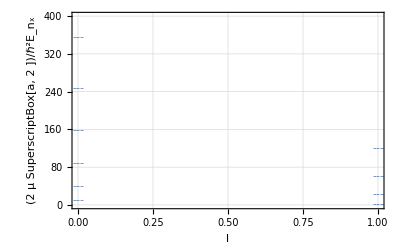

```mathematica
ThadPlot[ListPlot[elevelsX⟦;;10⟧,PlotRange->{0,400},PlotMarkers->"---"],{"l","(2  μ SuperscriptBox[a, 2 ])/ℏ^2E_n_x"}]
```

For n_y:

```mathematica
elevelsY=Table[{l,BesselJZero[-1+1/2 (1-2 l),n+1]^2//N},{l,0,3},{n,0,5}]~Flatten~1
```

{{0,2.4674},{0,22.2066},{0,61.685},{0,120.903},{0,199.859},{0,298.556},{1,7.83096},{1,7.83096},{1,37.4697},{1,86.8226},{1,155.912},{1,244.739},{2,15.6779},{2,55.5265},{2,15.6779},{2,55.5265},{2,114.825},{2,193.813},{3,25.8928},{3,76.2777},{3,145.626},{3,25.8928},{3,76.2777},{3,145.626}}

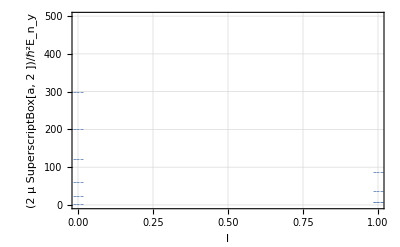

```mathematica
ThadPlot[ListPlot[elevelsY⟦;;10⟧,PlotRange->{0,500},PlotMarkers->"---"],{"l","(2  μ SuperscriptBox[a, 2 ])/ℏ^2E_n_y"}]
```